## Oldest Eigenvalue Algorithm: Jacobi reduce A=Aᵀ using G_2

Before the word “matrix” existed Jacobi needed to compute what would be called the eigenvalues of a real symmetric 7×7 matrix: there were only seven known planets at the time! He invented what is now called the Jacobi method!

This algorithm is still used when high precision small eigenvalues are important. It is also used on some specialized hardware.

#### Background and Code

We can diagonalize a symmetric 2 by 2 matrix using the Givens rotation (p1 | p2
-p2 | p1).   Lets work out the recipe!

```mathematica
AHat=({{p1, p2}, {-p2, p1}}).({{a11, a12}, {a12, a22}}).({{p1, -p2}, {p2, p1}});
MatrixForm[AHat]
```

(p1 (a11 p1+a12 p2)+p2 (a12 p1+a22 p2) | -p2 (a11 p1+a12 p2)+p1 (a12 p1+a22 p2)
p1 (a12 p1-a11 p2)+p2 (a22 p1-a12 p2) | -p2 (a12 p1-a11 p2)+p1 (a22 p1-a12 p2))

There are two values of p1 that work! Of course, we need to check that the expression under the square root is not negative if we want a real computation.

```mathematica
Solve[AHat⟦1,2⟧==0,p1]
```

{{p1→(a11 p2-a22 p2-√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)},{p1→(a11 p2-a22 p2+√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)}}

It is OK since a11^2+4 a12^2-2 a11 a22+a22^2=(a11-a22)^2+4 a12^2.  In practice, we should choose which solution we use carefully.  For now I am going to use the first one! Remember for the Givens matrices we need ||{p1,p2}||=1.

```mathematica
JMat[{{a11_,a12_},{a21_,a22_}}]:=Module[{p1,p2=1},
p1=(a11-a22-√((a11-a22)^2+4 a12^2))/(2 a12);
{p1,p2}=Normalize[{p1,p2}];
({{p1, p2}, {-p2, p1}})
]
```

As always test

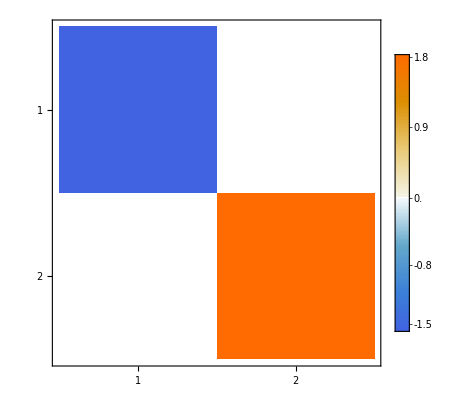

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
G=JMat[A];
GAGt=G.A.Gᵀ;
Map[MatrixForm,{G.Gᵀ,GAGt}];
MatrixPlot[Chop[GAGt],PlotLegends->Automatic]
```

To use this in a larger matrix we target a specific entry {i,j} and embed the appropriate tiny rotation in the identity matrix.

```mathematica
SetAttributes[BigJ,HoldFirst];
BigJ[A_,{i_,j_}]:=Module[{m=Length[A],G},
G=IdentityMatrix[m];
G⟦{i,j},{i,j}⟧=JMat[A⟦{i,j},{i,j}⟧];
G
]
```

As always test!

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
{i,j}={5,2};
G=BigJ[A,{i,j}];
GAGt=G.A.Gᵀ;
TabView[Map[MatrixPlot,Chop[{GAGt,G,G.Gᵀ,A}]]]
```

1234

So lets try to string a few of these together. It works just the way we expect if we are careful not to overlap!

```mathematica
m=7;
A=A0=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{3,4},{5,6}}}];
SetOptions[MatrixPlot, 
ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
```

123

If we overlap zeros that were made earlier they get messed up.

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7}}}];
SetOptions[MatrixPlot, ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
MatrixForm[A]
```

123456

(-1.7948 | -0.492756 | 0.440746 | 0.521403 | -0.362689 | 0.0495347 | 3.00822×10^-17
-0.492756 | 0.854924 | 0.577163 | -1.33747 | 0.519927 | 0.349474 | -0.193195
0.440746 | 0.577163 | 0.405321 | 0.0782387 | 1.52987 | -0.49153 | 0.0781847
0.521403 | -1.33747 | 0.0782387 | -0.541239 | 0.0364811 | -1.25305 | 0.522533
-0.362689 | 0.519927 | 1.52987 | 0.0364811 | 0.431994 | 0.445696 | 1.01881
0.0495347 | 0.349474 | -0.49153 | -1.25305 | 0.445696 | 0.990645 | -0.332373
-1.38778×10^-17 | -0.193195 | 0.0781847 | 0.522533 | 1.01881 | -0.332373 | 0.734139)

Jacobi (or more likely one of his helpers aka computers or computes) was doing this by hand and would have been painstakingly updating a block of numbers.

You would like to be done as fast as possible.

You can do any of the entries.

Which one should you do?

Jacobi’s plan was “Do the big ones first!”  This assumes that arithmetic is slow (it was then) and that it is fast (true for a small matrix) to find the biggest entry.  
https://en.wikipedia.org/wiki/Jacobi_eigenvalue_algorithm

```mathematica
SetAttributes[JacobiStep, HoldFirst]
JacobiStep[A_]:= Module[{AbsA=Abs[UpperTriangularize[A,1]],ij,G},
(* Find the largest non-diagonal entry *)
ij=Position[AbsA,Max[AbsA]]⟦1⟧;
(* Compute the Jacobi/Given rotation zapping the biggest entry *)
G=BigJ[A,ij];
(* Update A in place *)
A=G.A.Gᵀ;
(* No need to return anything! *)
]
```

As always test.

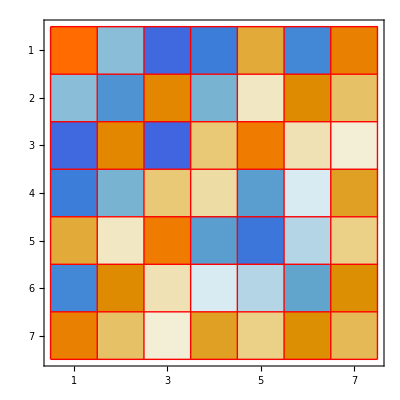
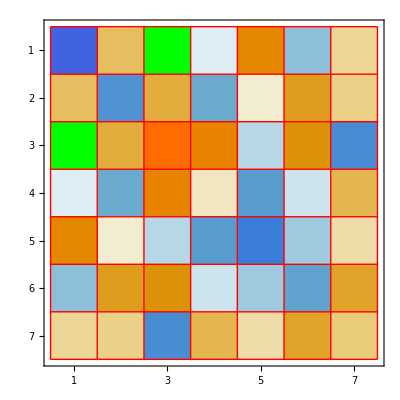

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
JacobiStep[A]
Map[MatrixPlot,Chop[{A0,A}]]
```

Now we can do a bunch and know that we are always targeting (and zeroing) large entries! This ensures it always makes progress and that it converges fast at the end!  Of course, copying and pasting is not a good plan! After a few steps the off-diagonal is looking fairly pale!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
TabView[{
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]]}]
```

12345678

Automation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=16;
TabView[Table[
JacobiStep[A];MatrixPlot[Chop[A]],
{MaxIter}]]
```

12345678910111213141516

#### Demo

Animation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=89;
ListAnimate[Table[
JacobiStep[A];MatrixPlot[Chop[A],PlotLabel->i],
{i,MaxIter}],8]
```

Things to note, something about our choices is pushing the negative eigenvalues up and the positive eigenvalues down!  Other choices will do other things! The common choice is to push the big (either positive or negative eigenvalues up) and the small eigenvalues down!

Like all eigenvalue algorithms this is iterative.  We are always interested in knowing if and how fast iterative algorithms  converge.  One way to measure how far a matrix is from diagonal is to square and then sum all the off-diagonal entries and then take a square root. Doing enough work to touch every entry of the matrix is called a sweep.  In other words, a sweep is “m” steps of the algorithm.

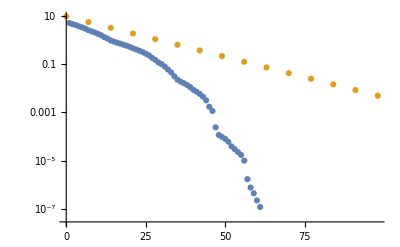

```mathematica
Γ[A_]:=√(Norm[A,"Frobenius"]^2-Norm[Diagonal[A]]^2)

m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=10^2;
Data=Table[
{i,JacobiStep[A];Γ[A]},
{i,MaxIter}];
C1Data=Table[
{k m,((1-1/m)^(m/2))^(k-1)Γ[A0]},
{k,0, Floor[MaxIter/m]}] ;

ListLogPlot[{Data,C1Data},PlotRange->All,
GridLines->{Range[0,MaxIter,m],Automatic}]
```

It is clear that the algorithm converges significantly faster than the simple bound.  There is a more complicated theorem that says that eventually the convergence is quadratic.  This means that for n big enough there is a k and a c satisfying
	Γ(A_(n+k))≤c (Γ(A_n))^2.
This means the last few steps are very quick. You can see the speed up at the very end.

This algorithm has more parallelism the standard “QR” Francis algorithm you are going to learn.  It has a developed very quaternionic G4 version that block diagonalizes symmetric matrices.  I am working on an alternative G4 and a G8 algorithm that make progress with a simple plan of “move the big entries up” that can work on non-symmetric matrices.

## New Eigenvalue Algorithm: reduce general A using G_4

The 2×2 matrix used in the Jacobi algorithm has a 4×4 analogue which we can use to make any specific entry of a matrix as large as possible. For any unit vector both recipes below give orthogonal matrices.

```mathematica
G41[{e0_,e1_,e2_,e3_}]:={
{e0,e1,e2,e3},
{e1,-e0,e3,-e2},
{e2,-e3,-e0,e1},
{e3,e2,-e1,-e0}}
G42[{e0_,e1_,e2_,e3_}]:={
{e0,e1,e2,e3},
{e1,-e0,-e3,e2},
{e2,e3,-e0,-e1},
{e3,-e2,e1,-e0}}
p=Normalize[RandomReal[{-1,1},4]];
Q1=G41[p]; Q2=G42[p];
Map[Norm,{Q1.Q1ᵀ-IdentityMatrix[4],Q2.Q2ᵀ-IdentityMatrix[4]}]
TabView[Map[MatrixForm,{Q1,Q2}]]
```

{2.498×10^-16,2.498×10^-16}

12

I want to make the 1-1 entry of  Q.A.Qᵀ as large as possible.  I symbolically compute 
	Q.A.Qᵀ
and extract the 1-1 entry. This is a pure quadratic in the argument of Q and I can automatically extract the matrix.

```mathematica
Q1=G41[{p1,p2,p3,p4}];
Q2=G42[{p1,p2,p3,p4}];
A=Array[a,{4,4}];
{const, lin, quad1}=CoefficientArrays[(Q1.A.Q1ᵀ)⟦1,1⟧,{p1,p2,p3,p4},"Symmetric"->True];
{const, lin, quad2}=CoefficientArrays[(Q2.A.Q2ᵀ)⟦1,1⟧,{p1,p2,p3,p4},"Symmetric"->True];
TabView[Map[MatrixForm,{quad1,quad2}]]
```

12

For both rotations the matrix for the 1-1 entry turns out to be B=1/2(A+Aᵀ).

We have worked out that the 1-1 entry in the new version with Q1=G41[p]
	A_new=Q1.A.Q1ᵀ
is p.B.p.  We want to choose p to make this as large as possible.  I want to compute
	p=argmax_(||p||=1)p.B.p
this is just the eigenvector associated with the largest eigenvalue.

```mathematica
A=A0=RandomReal[{-1,1},{4,4}];
B=A+Aᵀ;
{p}=Eigenvectors[B,1];
Q1=G41[p];
ANew=Q1.A.Q1ᵀ;
TabView[{
"A"->MatrixForm[A],
"ANew"->MatrixForm[ANew]}]
```

12

I can do a 7×7 problem by picking 4 indices and embedding the G4 matrix into a 7×7 identity matrix.

```mathematica
Clear[p1,p2,p3,p4]
BigG41[is_,ps_]:= Module[{Q},
Q=IdentityMatrix[7];
Q⟦is,is⟧=G41[ps];
Q]
BigG42[is_,ps_]:= Module[{Q},
Q=IdentityMatrix[7];
Q⟦is,is⟧=G42[ps];
Q]
is={1,2,3,4};
Q1=BigG41[is,{p1,p2,p3,p4}];
Q2=BigG42[is,{p1,p2,p3,p4}];
TabView[{
"Q1"->MatrixForm[Q1],"Q1ᵀ.Q1"->MatrixForm[Q1ᵀ.Q1],
"Q2"->MatrixForm[Q2],"Q2ᵀ.Q2"->MatrixForm[Q2ᵀ.Q2]
}]
```

1234

I can make the 1-1 entry of a big matrix as large as possible by picking 4 indices including 1 and using the appropriate Q in this recipe.

```mathematica
A=A0=RandomReal[{-1,1},{7,7}];
MaxIter=40;
Table[
is=Join[{1},RandomSample[Range[2,7],3]];
ASub=A⟦is,is⟧;
{p}=Eigenvectors[ASub+ASubᵀ,1];
Q1=BigG41[is,p];
A=Q1.A.Q1ᵀ;
A⟦1,1⟧,
{MaxIter}]
```

{-1.45451,-1.59237,-2.08154,-2.19661,-2.19755,-2.19759,-2.1976,-2.1976,-2.19763,-2.19763,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764,-2.19764}

It got stuck!  The reason it got stuck is that you need a product of both types of G4 to represent all rotations in ℝ^4.   For the folks who like quaternions the two matrix types match up with left and right hand quaternion multiplication.